## Definitions

```mathematica
ClearAll["Global`*"];
```

We want to study a variation of the classical Rosenzweig-MacArthur prey-predator model. The classical model describes the temporal variation of a resource R(t) and a consumer C(t):



r>0 is the rate constant, k>0 is the carrying capacity of the prey population, α>0 the attack rate, η>0 the handling rate, ϵ>0 an efficiency parameter, and β>0 is the mortality rate of the consumer.
We introduce an individual phenotypic variation through the quantitative trait x, with a normal distribution in the population centered on x̄ and of standard deviation σ:
.
The attack rate individual variation can be expressed as:
, with τ>0 the standard deviation of the distribution centered on θ_α>0. Since α>0, we also have α_max>0.
The handling rate is similarly described, although the “best” behaviour is for the minimum handling time:
, with ν>0 the standard deviation of the distribution centered on θ_η>0, η_max>0 and 0<η_min<=η_max.
The modified problem is thus:

```mathematica
(*Probability distribution*)
pdist[x_,X_,σ_]:=1/(√(2π σ))ⅇ^(-(x-X)^2/(2σ));
(*Attack rate*)
attack[x_,a_,α_,τ_]:=α ⅇ^(-(x-a)^2/(2 τ^2));
(*Handling rate*)
handling[x_,h_,ηmin_,ηmax_,ν_]:=ηmax-(ηmax-ηmin)ⅇ^(-(x-h)^2/(2 ν^2));
Manipulate[Plot[{attack[x,a,α,τ],handling[x,h,ηmin,ηmax,ν]},{x,0,10}],{{a,5},0.1, 10},{{h,5}, 0.1,10},{{α,1.5},0.01,3},{{ηmin,1},0.01,3},{{ηmax,2},0.01,3},{{τ,1},0.01,2},{{ν,1},0.01,2}]
```

The interaction rate has no analytical solution:

```mathematica
(*∫_(-∞)^∞ attack[x,a,α,τ]/(1+attack[x,a,α,τ]handling[x,h,ηmin,ηmax,ν])pdist[x,X,σ]ⅆx*)(*takes a long time to run since no solution*)
```

∫_(-∞)^∞ (ⅇ^(-(x-X)^2/(2 σ)-(-a+x)^2/(2 τ^2)) α)/(√(2 π) (1+ⅇ^(-(-a+x)^2/(2 τ^2)) α (ηmax+ⅇ^(-(-h+x)^2/(2 ν^2)) (-ηmax+ηmin))) √σ)ⅆx

Averaging the attack and handling rates introduces interesting new variables: d_α^2=(x̄-θ_α)^2 and d_η^2=(x̄-θ_η)^2, the squared distance between the mean trait in the population and the optimal value for attack and handling, respectively. The expressions of the average attack and handling rates are  and  respectively.

```mathematica
(*Average attack rate*)
∫_(-∞)^∞ attack[x,a,α,τ]pdist[x,X,σ]ⅆx
AvgAttack[a_,α_,τ_,X_,σ_]:=(ⅇ^(-(a-X)^2/(2 (σ+τ^2))) α)/(√σ √(1/σ+1/τ^2))
(*Subsituting a and X with da*)
AvgAttackD[da_,α_,τ_,σ_]:=AvgAttack[a,α,τ,X,σ]/.Solve[First[{da^2==(X-a)^2},{X,a}]][[1]] (*The two solution are identical*)
AvgAttackD[da,α,τ,σ]
```

ConditionalExpression[(ⅇ^(-(a-X)^2/(2 (σ+τ^2))) α)/(√σ √(1/σ+1/τ^2)), Re[1/σ+1/τ^2]>0]

(ⅇ^(-da^2/(2 (σ+τ^2))) α)/(√σ √(1/σ+1/τ^2))

```mathematica
(*Average handling rate*)
∫_(-∞)^∞ handling[x,h,ηmin,ηmax,ν]pdist[x,X,σ]ⅆx//FullSimplify
AvgHandling[h_,ηmin_,ηmax_,ν_,X_,σ_]:=((ⅇ^(-(h-X)^2/(2 (ν^2+σ))) (-ηmax+ηmin))/(√(1/ν^2+1/σ))+ηmax/(√(1/σ)))/(√σ)
(*Subsituting h and X with dh*)
AvgHandlingD[dh_,ηmin_,ηmax_,ν_,σ_]:=AvgHandling[h,ηmin,ηmax,ν,X,σ]/.Solve[First[{dh^2==(X-h)^2},{X,h}]][[1]](*The two solutions are identical*)
AvgHandlingD[dh,ηmin,ηmax,ν,σ]
```

(ηmax √(1/σ)+(ⅇ^(-(h-X)^2/(2 (ν^2+σ))) (-ηmax+ηmin))/(√(1/ν^2+1/σ) σ)) √σ

((ⅇ^(-dh^2/(2 (ν^2+σ))) (-ηmax+ηmin))/(√(1/ν^2+1/σ))+ηmax/(√(1/σ)))/(√σ)

```mathematica
(*Numerical functions needed for the graph*)
AvgAttackNum[da_?NumericQ,α_?NumericQ,τ_?NumericQ,σ_?NumericQ]:=(ⅇ^(-da^2/(2 (σ+τ^2))) α)/(√σ √(1/σ+1/τ^2))
AvgHandlingNum[dh_?NumericQ,ηmin_?NumericQ,ηmax_?NumericQ,ν_?NumericQ,σ_?NumericQ]:=((ⅇ^(-dh^2/(2 (ν^2+σ))) (-ηmax+ηmin))/(√(1/ν^2+1/σ))+ηmax/(√(1/σ)))/(√σ)
Manipulate[Plot[{AvgAttackNum[d,α,τ,σ],AvgHandlingNum[d,ηmin,ηmax,ν,σ]},{d,-5,5}],{{α,1.5},0.01,3},{{ηmin,1},0.01,3},{{ηmax,2},0.01,3},{{τ,1},0.01,2},{{ν,1},0.01,2},{{σ,1},0.01,4}]
```

## Jacobian method

This method allows to compute stability without having to numerically solve the whole system. It is described in more detail in the first Section, and applied iteratively to reproduce Figure 3 in the second.

## Introduction to the Jacobian method

The stability of a system can be checked around an equilibrium using the Jacobian method. Unfortunately, there’s no analytical solution to the equilibrium for this system:

```mathematica
f[R_,c_,r_,k_,a_,α_,τ_,h_,ηmin_,ηmax_,ν_,X_,σ_]:=r R(1-R/k)-(∫_(-∞)^∞ attack[x,a,α,τ]/(1+attack[x,a,α,τ]handling[x,h,ηmin,ηmax,ν]R)pdist[x,X,σ]ⅆx)R c;
g[R_,c_,ϵ_,β_,a_,α_,τ_,h_,ηmin_,ηmax_,ν_,X_,σ_]:=ϵ(∫_(-∞)^∞ attack[x,a,α,τ]/(1+attack[x,a,α,τ]handling[x,h,ηmin,ηmax,ν]R)pdist[x,X,σ]ⅆx)R c-β c;
(*sol=Solve[{f[R,c,r,k,a,α,τ,h,ηmin,ηmax,ν,X,σ]==0,g[R,c,ϵ,β,a,α,τ,h,ηmin,ηmax,ν,X,σ]==0},{R,c}] This lign doesn't converge, so don't run it*)
```

We thus have to search for a solution numerically. The equilibrium condition is:
, with .
The second equation for C^*≠0 yields . This can be used to find R^*. C^* is then found with the first equation: .

```mathematica
params={r->0.3,α->2,ηmax->2,ηmin->1,ϵ->0.5,τ->1,ν->1,k->1,β->0.1,X->3,a->2.5,h->2.5,σ->√3};
Int1[R_?NumericQ,a_?NumericQ,α_?NumericQ,τ_?NumericQ,h_?NumericQ,ηmin_?NumericQ,ηmax_?NumericQ,ν_?NumericQ,X_?NumericQ,σ_?NumericQ]:=NIntegrate[attack[x,a,α,τ]/(1+attack[x,a,α,τ]handling[x,h,ηmin,ηmax,ν]R)pdist[x,X,σ],{x,-∞,∞}]
FNum[R_?NumericQ,a_?NumericQ,α_?NumericQ,τ_?NumericQ,h_?NumericQ,ηmin_?NumericQ,ηmax_?NumericQ,ν_?NumericQ,X_?NumericQ,σ_?NumericQ,β_?NumericQ,ϵ_?NumericQ]:=R Int1[R,a,α,τ,h,ηmin,ηmax,ν,X,σ]-β/ϵ
Rsol=FindRoot[{(FNum[R,a,α,τ,h,ηmin,ηmax,ν,X,σ,β,ϵ]/.params)==0},{R,0.5}]
csol={c->(((r R(1-R/k))/(R Int1[R,a,α,τ,h,ηmin,ηmax,ν,X,σ]))/.params)/.Rsol}
```

{R→0.249008}

{c→0.280504}

We have a feasible solution, so there’s coexistence. Let’s now check what the stability of this solution looks like.

The Jacobian is defined as: J=(∂_R f | ∂_C f
∂_R g | ∂_C g). This can be formally done because in this case the integral over x and the derivative with respect to R can be inverted (dominating function: φ(x)=(α(x))^2 η(x)p(x)>=|∂_R ((α(x))/(1+α(x)η(x)R)p(x))|=((α(x))^2 η(x)p(x))/(1+α(x)η(x)R)^2 >=0 ). However, Mathematica doesn’t know that, so we do the derivation by hand:

```mathematica
Int2[R_?NumericQ,a_?NumericQ,α_?NumericQ,τ_?NumericQ,h_?NumericQ,ηmin_?NumericQ,ηmax_?NumericQ,ν_?NumericQ,X_?NumericQ,σ_?NumericQ]:=NIntegrate[attack[x,a,α,τ]/(1+attack[x,a,α,τ]handling[x,h,ηmin,ηmax,ν]R)pdist[x,X,σ](1-(attack[x,a,α,τ]handling[x,h,ηmin,ηmax,ν]R)/(1+attack[x,a,α,τ]handling[x,h,ηmin,ηmax,ν]R)),{x,-∞,∞}]
JacobiAtEq={
{r(1-(2R)/k)-c Int2[R,a,α,τ,h,ηmin,ηmax,ν,X,σ],
-R Int1[R,a,α,τ,h,ηmin,ηmax,ν,X,σ]},
{ϵ c Int2[R,a,α,τ,h,ηmin,ηmax,ν,X,σ],
ϵ R Int1[R,a,α,τ,h,ηmin,ηmax,ν,X,σ]-β}
}/.Join[params,Rsol,csol]
```

{{-0.00676221,-0.2},{0.0786788,2.77556×10^-17}}

We can now check the stability

```mathematica
det=Det[JacobiAtEq]
tr=Tr[JacobiAtEq]
```

0.0157358

-0.00676221

Here,  and  (meaning the real part of both eigenvalues are <0), so we’re in a case where the solution converges with time to the equilibrium we found earlier (R^*,C^*). Damped oscillations correspond to the complex eigenvalue case, while the nonoscillatory case correspond to real eigenvalues. Thus, we can check the sign of  (Δ>=0: real eigenvalues, Δ<0: complex eigenvalues).

```mathematica
tr^2-4det
```

-0.0628973

We are in the damped oscillation window! This is consistent with Figure 3 (parameters corresponding to the asterisk)!

## Figure 3 reproduction (iteration over d^2 and σ^2)

We can now try to reproduce Figure 3, by generalizing this method to (d^2,σ^2)∈[0,2.5]×[0,6].

### Classification and functions definition

The classification is as follows:
 - If R^*<=0 or C^*<=0, we are in the “Noncoexistence” domain (no feasible solution);
 - If R^*>0 and C^*>0, we are in one of the “Coexistence” domain;
 	- If , , and Δ>=0, we are in the “Coexistence: nonoscillatory” domain;
 	- If , , and Δ<0, we are in the “Coexistence: damped oscillations” domain;
 	- If , , we are in the “Coexistence: limit cycles” domain.
Let’s first define a function computing the equilibrium:

```mathematica
ClearAll["Global`*"];
pdist[x_,X_,σ_]:=1/(√(2π σ))ⅇ^(-(x-X)^2/(2σ));
attack[x_,a_,α_,τ_]:=α ⅇ^(-(x-a)^2/(2 τ^2));
handling[x_,h_,ηmin_,ηmax_,ν_]:=ηmax-(ηmax-ηmin)ⅇ^(-(x-h)^2/(2 ν^2));
Int1[R_?NumericQ,a_?NumericQ,α_?NumericQ,τ_?NumericQ,h_?NumericQ,ηmin_?NumericQ,ηmax_?NumericQ,ν_?NumericQ,X_?NumericQ,σ_?NumericQ]:=NIntegrate[attack[x,a,α,τ]/(1+attack[x,a,α,τ]handling[x,h,ηmin,ηmax,ν]R)pdist[x,X,σ],{x,-∞,∞}];
Int2[R_?NumericQ,a_?NumericQ,α_?NumericQ,τ_?NumericQ,h_?NumericQ,ηmin_?NumericQ,ηmax_?NumericQ,ν_?NumericQ,X_?NumericQ,σ_?NumericQ]:=NIntegrate[attack[x,a,α,τ]/(1+attack[x,a,α,τ]handling[x,h,ηmin,ηmax,ν]R)pdist[x,X,σ](1-(attack[x,a,α,τ]handling[x,h,ηmin,ηmax,ν]R)/(1+attack[x,a,α,τ]handling[x,h,ηmin,ηmax,ν]R)),{x,-∞,∞}];
FNum[R_?NumericQ,a_?NumericQ,α_?NumericQ,τ_?NumericQ,h_?NumericQ,ηmin_?NumericQ,ηmax_?NumericQ,ν_?NumericQ,X_?NumericQ,σ_?NumericQ,β_?NumericQ,ϵ_?NumericQ]:=R Int1[R,a,α,τ,h,ηmin,ηmax,ν,X,σ]-β/ϵ;
X=3;(*arbitrary*)
paramsGen={r->0.3,α->2,ηmax->2,ηmin->1,ϵ->0.5,τ->1,ν->1,k->1,β->0.1,X->X};
EqSol[dval_?NumericQ,σval_?NumericQ]:=Module[{paramsSpec,FNumVal,Rsol,csol},
paramsSpec=Join[paramsGen,{a->X-dval,h->X-dval,σ->σval}];
FNumVal[R_?NumericQ]:=FNum[R,a,α,τ,h,ηmin,ηmax,ν,X,σ,β,ϵ]/.paramsSpec;
Rsol=FindRoot[{FNumVal[R]==0},{R,0.5}];
csol={c->(((r R(1-R/k))/(R Int1[R,a,α,τ,h,ηmin,ηmax,ν,X,σ]))/.paramsSpec)/.Rsol};
{R,c}/.Join[Rsol,csol]
]
```

Let’s check with the parameters we already looked at:

```mathematica
testSol=EqSol[0.5,√3]
```

{0.249008,0.280504}

Perfect! Now let’s write a function that computes the det and tr from the equilibrium:

```mathematica
DetTr[dval_?NumericQ,σval_?NumericQ,sol_]:=Module[{Rsol,csol,paramsSpec,JacobiAtEq},
Rsol=sol[[1]];
csol=sol[[2]];
paramsSpec=Join[paramsGen,{a->X-dval,h->X-dval,σ->σval}];
JacobiAtEq={
{r(1-(2R)/k)-c Int2[R,a,α,τ,h,ηmin,ηmax,ν,X,σ],
-R Int1[R,a,α,τ,h,ηmin,ηmax,ν,X,σ]},
{ϵ c Int2[R,a,α,τ,h,ηmin,ηmax,ν,X,σ],
ϵ R Int1[R,a,α,τ,h,ηmin,ηmax,ν,X,σ]-β}
}/.Join[paramsSpec,{R->Rsol,c->csol}];
{Det[JacobiAtEq],Tr[JacobiAtEq]}
]
```

Let’s check as before:

```mathematica
testMat=DetTr[0.5,√3,testSol]
```

{0.0157358,-0.00676221}

Perfect! Let’s move on to the automatic classification function. It will return:
 - 0 if noncoexistence
 - 1 if coexistence: nonoscillatory
 - 2 if coexistence: damped oscillations
 - 3 if coexistence: limit cycles

```mathematica
Classifying[dval_?NumericQ,σval_?NumericQ]:=Module[{sol,coeffs},
sol=EqSol[dval,σval];
If[sol[[1]]>0&&sol[[2]]>0,
(*True: coexistence*)
coeffs=DetTr[dval,σval,sol];
If[coeffs[[1]]>0&&coeffs[[2]]<0,
(*True: no limit cycles*)
If[coeffs[[2]]^2-4coeffs[[1]]>=0,
(*True: nonoscillatory*)
1,
(*False: damped oscillations*)
2
],
(*False: limit cycles*)
3
],
(*False: no coexistence*)
0
]
]
```

Last check, it should return 2:

```mathematica
Classifying[0.5,√3]
```

2

Amazing! Let’s move on.

### Iteration to create the plot

We can now create a grid of d and σ, iterate the classification and create the plot.

```mathematica
dvals=Range[0.01,2.5,0.02];
σvals=Range[0.01,6,0.05];
Length[dvals]Length[σvals]
```

15000

```mathematica
data=ParallelTable[
Classifying[d,σ],
{d,dvals},
{σ,σvals}
];
```

```mathematica
leg=SwatchLegend[
{Black,White,LightGray,Gray},
{"Noncoexistence","Coexistence: nonoscillatory","Coexistence: damped oscillations","Coexistence: limit cycles"},
LegendMarkers->"Rectangle"
];
Legended[
ArrayPlot[data,
DataReversed->True,
ColorRules->{
0->Black,
1->White,
2->LightGray,
3->Gray
},
Frame->True,
FrameTicks->{
Table[{i,Round[dvals[[i]],0.01]},{i,1,Length[dvals],25}],
Table[{i,Round[σvals[[i]],0.01]},{i,1,Length[σvals],25}]
},
FrameLabel->{"Phenomtypic mismatch (d^2)","Individual variation (σ^2)"},
Mesh->False,
AspectRatio->1/1.5
],
leg
]
```

-Graphics-

This plot took 5’45 to compute.
This is a bit different from the original figure: the “Coexistence: damped oscillations” domain looks a lot greater, which is due to the fact that the “manual” criterium for this on the original figure was wrong.
Indeed, the last example on the original figure, which is supposed to be nonoscillatory, has one (greatly damped) oscillation. Here, the right formalism is taken, which is stricter.
A similar effect can be observed for the “Noncoexistence” domain, which looks smaller here. However, we can suppose that the “manual” criterium to distinguish between “Coexistence: nonoscillatory” and “Noncoexistence” fails when there is an equilibrium with R^*≠0 and C^*≠0, but with very slow convergence, which would happen very late.

### Optimization of the previous sections

Let’s change a few things to obtain this plot quicker and get a better resolution without hours of computation.
What’s new?
 - NIntegrate options:
 	- Method: “GlobalAdaptive”
 	- MaxRecursion: 20 (10 was not enough)
 	- AccuracyGoal: 6 (4 was not enough)
 	- PrecisionGoal: 6
 - FindRoot options. This is important because if the solution is wrong, then the stability is also wrong:
 	- Method: “Secant” (default is “Newton”, slower)
 	- WorkingPrecision: 20
 	- AccuracyGoal: 8
 	- PrecisionGoal: 8
 	- MaxIteration: 100
 - Integrals functions are memoized, this means for each set of parameters, the value is stored, so that it’s not computed twice. This is especially important for `Int1` which is called in the root finding algorithm, so possibly lots of times. The formalism is `f[x_?NumericQ,y_?NumericQ,z_?NumericQ]:=f[x,y,z]=....08`.
 - The integration limits are set to , since  is a normal law of standard deviation σ. However, this caused huge instability very close to σ=0, so for σ<1, the integration limits are set to .

```mathematica
(* --- GLOBAL SETTINGS --- *)
ClearAll["Global`*"];
SetOptions[NIntegrate,Method->"GlobalAdaptive",MaxRecursion->20,AccuracyGoal->6,PrecisionGoal->6];

(* --- FUNCTIONS DEFINITIONS --- *)
ClearAll[pdist,attack,handling];
pdist[x_,X_,σ_]:=1/(√(2π σ))ⅇ^(-(x-X)^2/(2σ));
attack[x_,a_,α_,τ_]:=α ⅇ^(-(x-a)^2/(2 τ^2));
handling[x_,h_,ηmin_,ηmax_,ν_]:=ηmax-(ηmax-ηmin)ⅇ^(-(x-h)^2/(2 ν^2));

(* --- MEMOIZED INTEGRALS --- *)
ClearAll[Int1,Int2];
Int1[R_?NumericQ,a_?NumericQ,α_?NumericQ,τ_?NumericQ,h_?NumericQ,ηmin_?NumericQ,ηmax_?NumericQ,ν_?NumericQ,X_?NumericQ,σ_?NumericQ]:=
Int1[R,a,α,τ,h,ηmin,ηmax,ν,X,σ]=Module[{xmin=X-5σ,xmax=X+5σ},
NIntegrate[attack[x,a,α,τ]/(1+attack[x,a,α,τ]handling[x,h,ηmin,ηmax,ν]R)pdist[x,X,σ],
If[σ<1,(* adaptive integration limits, because when σ is too small, numerical integration is wrong*)
{x,X-5,X+5},
{x,xmin,xmax}
]
]
];
Int2[R_?NumericQ,a_?NumericQ,α_?NumericQ,τ_?NumericQ,h_?NumericQ,ηmin_?NumericQ,ηmax_?NumericQ,ν_?NumericQ,X_?NumericQ,σ_?NumericQ]:=Int2[R,a,α,τ,h,ηmin,ηmax,ν,X,σ]=Module[{xmin=X-5σ,xmax=X+5σ},
NIntegrate[
With[
{A=attack[x,a,α,τ],H=handling[x,h,ηmin,ηmax,ν]},
A/(1+A H R)pdist[x,X,σ](1-(A H R)/(1+A H R))
],
If[σ<1,(* adaptive integration limits, because when σ is too small, numerical integration is wrong*)
{x,X-5,X+5},
{x,xmin,xmax}
]
]
];

(* --- MODEL DEFINITION --- *)
ClearAll[FNum,EqSol,DetTr,Classifying];
FNum[R_?NumericQ,a_?NumericQ,α_?NumericQ,τ_?NumericQ,h_?NumericQ,ηmin_?NumericQ,ηmax_?NumericQ,ν_?NumericQ,X_?NumericQ,σ_?NumericQ,β_?NumericQ,ϵ_?NumericQ]:=R Int1[R,a,α,τ,h,ηmin,ηmax,ν,X,σ]-β/ϵ;
X=3;(*arbitrary, can be any real number*)
paramsGen={r->0.3,α->2,ηmax->2,ηmin->1,ϵ->0.5,τ->1,ν->1,k->1,β->0.1,X->X};

EqSol[dval_?NumericQ,σval_?NumericQ]:=Module[{paramsSpec,FNumVal,Rsol,csol},
paramsSpec=Join[paramsGen,{a->X-dval,h->X-dval,σ->σval}];
FNumVal[R_?NumericQ]:=FNum[R,a,α,τ,h,ηmin,ηmax,ν,X,σ,β,ϵ]/.paramsSpec;
Rsol=Quiet@FindRoot[
{FNumVal[R]==0},{R,0.5},
Method->"Secant", WorkingPrecision->20,AccuracyGoal->8,PrecisionGoal->8,MaxIterations->100
];
csol={c->(((r R(1-R/k))/(R Int1[R,a,α,τ,h,ηmin,ηmax,ν,X,σ]))/.paramsSpec)/.Rsol};
{R,c}/.Join[Rsol,csol]
]

DetTr[dval_?NumericQ,σval_?NumericQ,sol_]:=Module[{Rsol,csol,paramsSpec,JacobiAtEq},
Rsol=sol[[1]];
csol=sol[[2]];
paramsSpec=Join[paramsGen,{a->X-dval,h->X-dval,σ->σval}];
JacobiAtEq={
{r(1-(2R)/k)-c Int2[R,a,α,τ,h,ηmin,ηmax,ν,X,σ],
-R Int1[R,a,α,τ,h,ηmin,ηmax,ν,X,σ]},
{ϵ c Int2[R,a,α,τ,h,ηmin,ηmax,ν,X,σ],
ϵ R Int1[R,a,α,τ,h,ηmin,ηmax,ν,X,σ]-β}
}/.Join[paramsSpec,{R->Rsol,c->csol}];
{Det[JacobiAtEq],Tr[JacobiAtEq]}
]

Classifying[dval_?NumericQ,σval_?NumericQ]:=Module[{sol,coeffs},
sol=EqSol[dval,σval];
If[VectorQ[sol,NumericQ]&&sol[[1]]>0&&sol[[2]]>0,
(*True: coexistence*)
coeffs=DetTr[dval,σval,sol];
Which[
coeffs[[1]]<0,0(*noncoexistence*),
coeffs[[1]]>=0&&coeffs[[2]]<0&&coeffs[[2]]^2-4coeffs[[1]]>=0,1,(*nonoscillatory*)
coeffs[[1]]>=0&&coeffs[[2]]<0&&coeffs[[2]]^2-4coeffs[[1]]<0,2,(*damped oscillations*)
coeffs[[1]]>=0&&coeffs[[2]]>=0,3(*limit cycles*)
],
(*False: noncoexistence*)
0
]
];

(* --- PARALLEL SCAN --- *)
dvals=Range[0,2.5,0.02];
σvals=Range[0.01,6,0.05];
DistributeDefinitions[pdist,attack,handling,Int1,Int2,FNum,EqSol,DetTr,Classifying,paramsGen,X];
LaunchKernels[];
data=ParallelTable[
Classifying[d,σ],
{d,dvals},
{σ,σvals}
];

leg=SwatchLegend[
{Black,White,LightGray,Gray},
{"Noncoexistence","Coexistence: nonoscillatory","Coexistence: damped oscillations","Coexistence: limit cycles"},
LegendMarkers->"Rectangle"
];
Legended[
ArrayPlot[data,
DataReversed->True,
ColorRules->{
0->Black,
1->White,
2->LightGray,
3->Gray
},
Frame->True,
FrameTicks->{
Table[{i,Round[dvals[[i]],0.01]},{i,26,Length[dvals],25}],
Table[{i,Round[σvals[[i]],0.01]},{i,20,Length[σvals],20}]
},
FrameLabel->{"Phenotypic mismatch (d^2)","Individual variation (σ^2)"},
Mesh->False,
AspectRatio->1/1.5
],
leg
]
```

LaunchKernels::nodef: Some parallel subkernels are already running. Not launching default kernels again.

-Graphics-

This plot took 2’40, so 2.2 times faster.

```mathematica
N[(5*60+45)/(2*60+40)]
```

2.15625

Let’s increase the resolution. d:×4 (step=0.005), σ:×5 (step=0.01) →×20~53’.

```mathematica
(* --- GLOBAL SETTINGS --- *)
ClearAll["Global`*"];
SetOptions[NIntegrate,Method->"GlobalAdaptive",MaxRecursion->20,AccuracyGoal->6,PrecisionGoal->6];

(* --- FUNCTIONS DEFINITIONS --- *)
ClearAll[pdist,attack,handling];
pdist[x_,X_,σ_]:=1/(√(2π σ))ⅇ^(-(x-X)^2/(2σ));
attack[x_,a_,α_,τ_]:=α ⅇ^(-(x-a)^2/(2 τ^2));
handling[x_,h_,ηmin_,ηmax_,ν_]:=ηmax-(ηmax-ηmin)ⅇ^(-(x-h)^2/(2 ν^2));

(* --- MEMOIZED INTEGRALS --- *)
ClearAll[Int1,Int2];
Int1[R_?NumericQ,a_?NumericQ,α_?NumericQ,τ_?NumericQ,h_?NumericQ,ηmin_?NumericQ,ηmax_?NumericQ,ν_?NumericQ,X_?NumericQ,σ_?NumericQ]:=
Int1[R,a,α,τ,h,ηmin,ηmax,ν,X,σ]=Module[{xmin=X-5σ,xmax=X+5σ},
NIntegrate[attack[x,a,α,τ]/(1+attack[x,a,α,τ]handling[x,h,ηmin,ηmax,ν]R)pdist[x,X,σ],
If[σ<1,(* adaptive integration limits, because when σ is too small, numerical integration is wrong*)
{x,X-5,X+5},
{x,xmin,xmax}
]
]
];
Int2[R_?NumericQ,a_?NumericQ,α_?NumericQ,τ_?NumericQ,h_?NumericQ,ηmin_?NumericQ,ηmax_?NumericQ,ν_?NumericQ,X_?NumericQ,σ_?NumericQ]:=Int2[R,a,α,τ,h,ηmin,ηmax,ν,X,σ]=Module[{xmin=X-5σ,xmax=X+5σ},
NIntegrate[
With[
{A=attack[x,a,α,τ],H=handling[x,h,ηmin,ηmax,ν]},
A/(1+A H R)pdist[x,X,σ](1-(A H R)/(1+A H R))
],
If[σ<1,(* adaptive integration limits, because when σ is too small, numerical integration is wrong*)
{x,X-5,X+5},
{x,xmin,xmax}
]
]
];

(* --- MODEL DEFINITION --- *)
ClearAll[FNum,EqSol,DetTr,Classifying];
FNum[R_?NumericQ,a_?NumericQ,α_?NumericQ,τ_?NumericQ,h_?NumericQ,ηmin_?NumericQ,ηmax_?NumericQ,ν_?NumericQ,X_?NumericQ,σ_?NumericQ,β_?NumericQ,ϵ_?NumericQ]:=R Int1[R,a,α,τ,h,ηmin,ηmax,ν,X,σ]-β/ϵ;
X=3;(*arbitrary, can be any real number*)
paramsGen={r->0.3,α->2,ηmax->2,ηmin->1,ϵ->0.5,τ->1,ν->1,k->1,β->0.1,X->X};

EqSol[dval_?NumericQ,σval_?NumericQ]:=Module[{paramsSpec,FNumVal,Rsol,csol},
paramsSpec=Join[paramsGen,{a->X-dval,h->X-dval,σ->σval}];
FNumVal[R_?NumericQ]:=FNum[R,a,α,τ,h,ηmin,ηmax,ν,X,σ,β,ϵ]/.paramsSpec;
Rsol=Quiet@FindRoot[
{FNumVal[R]==0},{R,0.5},
Method->"Secant", WorkingPrecision->20,AccuracyGoal->8,PrecisionGoal->8,MaxIterations->100
];
csol={c->(((r R(1-R/k))/(R Int1[R,a,α,τ,h,ηmin,ηmax,ν,X,σ]))/.paramsSpec)/.Rsol};
{R,c}/.Join[Rsol,csol]
]

DetTr[dval_?NumericQ,σval_?NumericQ,sol_]:=Module[{Rsol,csol,paramsSpec,JacobiAtEq},
Rsol=sol[[1]];
csol=sol[[2]];
paramsSpec=Join[paramsGen,{a->X-dval,h->X-dval,σ->σval}];
JacobiAtEq={
{r(1-(2R)/k)-c Int2[R,a,α,τ,h,ηmin,ηmax,ν,X,σ],
-R Int1[R,a,α,τ,h,ηmin,ηmax,ν,X,σ]},
{ϵ c Int2[R,a,α,τ,h,ηmin,ηmax,ν,X,σ],
ϵ R Int1[R,a,α,τ,h,ηmin,ηmax,ν,X,σ]-β}
}/.Join[paramsSpec,{R->Rsol,c->csol}];
{Det[JacobiAtEq],Tr[JacobiAtEq]}
]

Classifying[dval_?NumericQ,σval_?NumericQ]:=Module[{sol,coeffs},
sol=EqSol[dval,σval];
If[VectorQ[sol,NumericQ]&&sol[[1]]>0&&sol[[2]]>0,
(*True: coexistence*)
coeffs=DetTr[dval,σval,sol];
Which[
coeffs[[1]]<0,0(*noncoexistence*),
coeffs[[1]]>=0&&coeffs[[2]]<0&&coeffs[[2]]^2-4coeffs[[1]]>=0,1,(*nonoscillatory*)
coeffs[[1]]>=0&&coeffs[[2]]<0&&coeffs[[2]]^2-4coeffs[[1]]<0,2,(*damped oscillations*)
coeffs[[1]]>=0&&coeffs[[2]]>=0,3(*limit cycles*)
],
(*False: noncoexistence*)
0
]
];

(* --- PARALLEL SCAN --- *)
dvals=Range[0,2.5,0.005];
σvals=Range[0.01,6,0.01];
DistributeDefinitions[pdist,attack,handling,Int1,Int2,FNum,EqSol,DetTr,Classifying,paramsGen,X];
LaunchKernels[];
data=ParallelTable[
Classifying[d,σ],
{d,dvals},
{σ,σvals}
];

(* --- EXPORTING RESULT --- *)
dataWithCols=Prepend[data,σvals];
dataWithHeader=MapThread[Prepend,{dataWithCols,Prepend[dvals,"d^2\\sigma^2"]}];
dataDir="D:\\OneDrive - agroparistech.fr\\predator-prey-ecotox-vi\\outputs\\data\\";
If[!DirectoryQ[dataDir],CreateDirectory[dataDir]];
Export[dataDir<>"fig_3_data.csv",dataWithHeader];
```

Here’s the plot:

```mathematica
ClearAll["Global`*"];
(* --- IMPORTING RESULTS --- *)
dataDir="D:\\OneDrive - agroparistech.fr\\predator-prey-ecotox-vi\\outputs\\data\\";
raw=Import[dataDir<>"fig_3_data.csv"];
dvals=ToExpression/@Rest[First[raw]];
σvals=ToExpression/@Rest[raw[[All,1]]];
data=ToExpression/@raw[[2;;,2;;]];

(* --- DEFINING PLOT --- *)
leg=SwatchLegend[
{Black,White,LightGray,Gray},
{"Noncoexistence","Coexistence: nonoscillatory","Coexistence: damped oscillations","Coexistence: limit cycles"},
LegendMarkers->"Rectangle"
];
plot=Legended[
ArrayPlot[data,
DataReversed->True,
ColorRules->{
0->Black,
1->White,
2->LightGray,
3->Gray
},
Frame->True,
FrameTicks->{
Table[{i,Round[σvals[[i]],0.01]},{i,101,Length[dvals],100}],
Table[{i,Round[dvals[[i]],0.01]},{i,100,Length[σvals],100}]
},
FrameLabel->{"Phenotypic mismatch (d^2)","Individual variation (σ^2)"},
Mesh->False,
AspectRatio->1/1.5
],
leg
]

(* --- EXPORTING PLOT --- *)
plotDir="D:\\OneDrive - agroparistech.fr\\predator-prey-ecotox-vi\\outputs\\figs\\";
If[!DirectoryQ[plotDir],CreateDirectory[plotDir]];
Export[plotDir<>"fig_3_repro.pdf",plot];
```

-Graphics-

## Dose-response simulations

Let’s move on to adding a pesticide concentration, and computing the response of the predator-prey system.

## Dose-response functions

Here are the defined the (individual) dose-response functions of a compound on a given parameter:

The idea here is to investigate the impact of a pesticide on a predator-prey ecosystem.

```mathematica
ClearAll[DRLogRNFun,DRFunLog,DRFunLogExp];

(*Equivalent to DR_logRN_fun*)
DRLogRNFun[Dose_,Rmin_,Rmax_,beta_,NEC_]:=Module[{logyhat,yhat},logyhat=Rmin+(Rmax-Rmin)*Exp[-Exp[beta]*(Dose-NEC)*Boole[Dose>NEC]];
yhat=Exp[logyhat];
yhat]

(*Equivalent to DR_fun_log*)
DRFunLog[Dose_,alpha_,beta_,NEC_]:=Piecewise[{{Log[alpha],Dose<NEC},{Log[alpha]-Exp[beta]*(Dose-NEC),Dose>=NEC}}]

(*Equivalent to DR_fun_log_exp*)
DRFunLogExp[Dose_,alpha_,beta_,NEC_]:=Exp[DRFunLog[Dose,alpha,beta,NEC]]
```

## Dose-response simulations

We will firstly generate a population of 10000 individuals, each with a different attack rate α.
Each individual also has a different minimal pesticide concentration above which the attack rate starts to decay.
The deviation among the population is of the mean.

```mathematica
(* --- GLOBAL PARAMETERS --- *)
alpha=100;
beta=-3.5;
Dose=Range[0,100,1];
NEC=25;

nID=10000;
CVi=0.2;
sigma=0.08;
```

Here is the individual dose-response function:

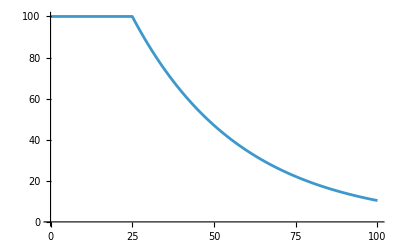

```mathematica
Manipulate[
Plot[DRFunLogExp[d,α,β,Cmax],{d,0,100}],
{{α,alpha},10, 200},{{β,beta},-10,-1},{{Cmax,NEC},5,80}
]
(*Check the baseline deterministic dose–response function*)
baseline=Table[
{d,DRFunLogExp[d,alpha,beta,NEC]},
{d,Dose}
];
ListLinePlot[baseline]
```

Let’s first generate all 10000 individuals, one set with positive correlation between α and NEC, another with negative correlation:

```mathematica
ClearAll[GenerateIndividuals];
GenerateIndividuals[rhoAlphaNEC_]:=Module[{Mu,sigmas,rhoMat,Sigma,dist,samples},
Mu={alpha,NEC};
sigmas={alpha*CVi,NEC*CVi};
rhoMat={{1,rhoAlphaNEC},{rhoAlphaNEC,1}};
Sigma=DiagonalMatrix[sigmas].rhoMat.DiagonalMatrix[sigmas];
dist=MultinormalDistribution[Mu,Sigma];
samples=RandomVariate[dist,nID];
Table[
<|"alpha"->samples[[i,1]],
"beta"->beta,(*fixed constant*)
"NEC"->samples[[i,2]],
"ID"->i|>,
{i,nID}
]
]
SeedRandom[42];
rhoAlphaNEC=0.9;
individualsPos=GenerateIndividuals[rhoAlphaNEC];
individualsNeg=GenerateIndividuals[-rhoAlphaNEC];
```

Here are the two populations distributions:

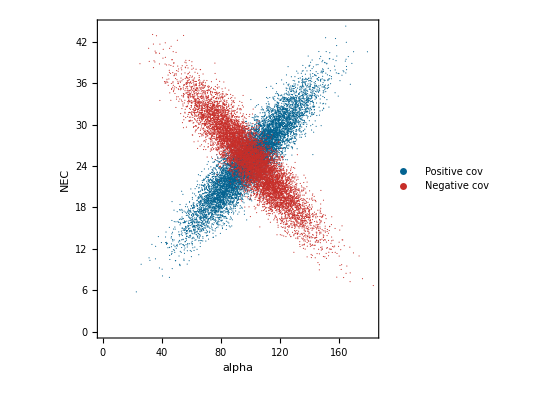

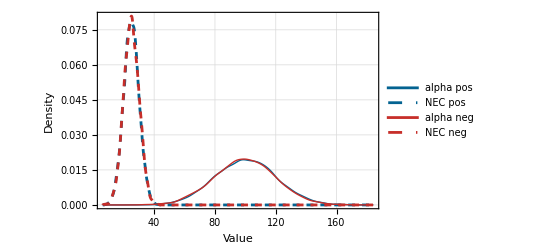

```mathematica
dataPos=individualsPos[[All,{"alpha","NEC"}]]/.assoc_Association:>{assoc["alpha"], assoc["NEC"]};
dataNeg=individualsNeg[[All,{"alpha","NEC"}]]/.assoc_Association:>{assoc["alpha"],assoc["NEC"]};
ListPlot[
{dataPos,dataNeg},
PlotStyle->{
Directive[RGBColor[0.01,0.39,0.57],PointSize[0.002]],(*blue tone*)
Directive[RGBColor[0.78,0.18,0.16],PointSize[0.002]]   (*red tone*)
},
Frame->True,FrameLabel->{"alpha","NEC"},Axes->False,AspectRatio->1,PlotLegends->{"Positive cov","Negative cov"}
]
SmoothHistogram[
{individualsPos[[All,"alpha"]],individualsPos[[All,"NEC"]],individualsNeg[[All,"alpha"]],individualsNeg[[All,"NEC"]]},
PlotLegends->{"alpha pos","NEC pos","alpha neg","NEC neg"},
PlotRange->All,
FrameLabel->{"Value","Density"},
PlotTheme->"Detailed",
PlotStyle->{
Directive[RGBColor[0.01,0.39,0.57],Thick],
Directive[RGBColor[0.01,0.39,0.57],Dashed],
Directive[RGBColor[0.78,0.18,0.16],Thick],
Directive[RGBColor[0.78,0.18,0.16],Dashed]
}
]
```

We can now compute the population distribution for each dose, and plot the mean  and standard deviation σ of the attack rate α for varying concentrations.

QUESTION : by doing this, it’s α_max and  that change? Not ?

```mathematica
ClearAll[SimulateDoseResponse];
SimulateDoseResponse[individuals_List]:=Module[{records,data},
records=Flatten[
Table[
With[{a=ind["alpha"],b=ind["beta"],n=ind["NEC"]},
Table[
Module[{logyhat,yhat,y},
logyhat=DRFunLog[d,a,b,n];
yhat=Exp[logyhat];
y=RandomVariate[LogNormalDistribution[logyhat,sigma]];
<|"ID"->ind["ID"],"Dose"->d,"logyhat"->logyhat,"yhat"->yhat,"y"->y|>],{d,Dose}
]
],{ind,individuals}]
,1
];
data=GroupBy[records,#Dose&];
(*Compute mean and sd per Dose*)
Table[
With[{vals=data[d]},
<|"Dose"->d,"yhatMean"->Mean[vals[[All,"yhat"]]],"yhatSD"->StandardDeviation[vals[[All,"yhat"]]]|>
],{d,Keys[data]}
]
];
```

```mathematica
(*Positive covariance between alpha and NEC*)
summaryPos=SimulateDoseResponse[individualsPos];
(*Negative covariance between alpha and NEC*)
summaryNeg=SimulateDoseResponse[individualsNeg];
```

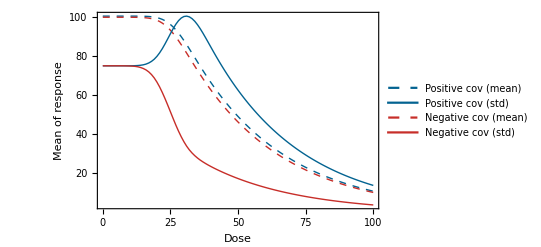

```mathematica
(*Mean and SD table for each Dose*)
meanPos=summaryPos[[All]]/.assoc_Association:>{assoc["Dose"],assoc["yhatMean"]};
meanNeg=summaryNeg[[All]]/.assoc_Association:>{assoc["Dose"],assoc["yhatMean"]};
stdPos=summaryPos[[All]]/.assoc_Association:>{assoc["Dose"],assoc["yhatSD"]};
stdNeg=summaryNeg[[All]]/.assoc_Association:>{assoc["Dose"],assoc["yhatSD"]};
(*Find y-range for scaling*)
ymin1=0;
ymax1=Max[meanPos[[All,2]]];
ymin2=0;
ymax2=Max[stdPos[[All,2]]];
(*Function to rescale SD to mean range for plotting*)
rescale[y_]:=Rescale[y,{ymin2,ymax2},{ymin1,ymax1}];
(*Create scaled SD data*)
stdPosScaled=stdPos/. {x_,y_}:>{x,rescale[y]};
stdNegScaled=stdNeg/. {x_,y_}:>{x,rescale[y]};
(*Helper for round-number ticks*)
niceTicks[min_,max_,step_]:=Table[
{t,ToString[Round[t]]},
{t,Ceiling[min/step]*step,Floor[max/step]*step,step}
];
(*Step sizes*)
stepMean=Round[(ymax1-ymin1)/5,5];
stepSD=Round[(ymax2-ymin2)/5,5];
(*Left ticks (mean)*)
leftTicks=niceTicks[ymin1,ymax1,stepMean];

(*Right ticks (SD)—force numeric positions*)
valsSD=Range[
Ceiling[ymin2/stepSD]*stepSD,
Floor[ymax2/stepSD]*stepSD,
stepSD
];
rightTicks=Table[
{N[rescale[v]],ToString[Round[v]]},
{v,valsSD}
];
(*Colors*)
colPos=RGBColor[0.01,0.39,0.57];
colNeg=RGBColor[0.78,0.18,0.16];
(*Define the legend separately*)
legend=LineLegend[
{
Directive[colPos,Dashed,Thick],
Directive[colPos,Thick],
Directive[colNeg,Dashed,Thick],
Directive[colNeg,Thick]
},
{
"Positive cov (mean)",
"Positive cov (std)",
"Negative cov (mean)",
"Negative cov (std)"
},
LegendFunction->"Frame",
LabelStyle->{FontSize->9,FontFamily->"Helvetica"},
LegendLayout->"Column",
LegendMargins->2,
LegendMarkerSize->18
];
(*Combined plot*)
dualPlot=Show[
{
ListLinePlot[
{meanPos,meanNeg},
PlotStyle->{
Directive[colPos,Dashed,Thick],
Directive[colNeg,Dashed,Thick]
},
Axes->False,
Frame->True,
FrameTicks->{{leftTicks,rightTicks},{Automatic,None}},
FrameLabel->{{"Mean of response","Standard deviation of response"},{"Dose",""}},
PlotRange->All,
ImagePadding->25
],
ListLinePlot[
{stdPosScaled,stdNegScaled},
PlotStyle->{
Directive[colPos,Thick],
Directive[colNeg,Thick]
},
Axes->False,
Frame->True,
FrameTicks->{{None,rightTicks},{None,None}},
PlotRange->{{Min[meanPos[[All,1]]],Max[meanPos[[All,1]]]},{ymin1,ymax1}},
ImagePadding->25
]
},
PlotRange->All,
ImagePadding->35,
Epilog->{
Inset[legend,Scaled[{0.8,0.7}]]
}
]
```

```mathematica
(* --- EXPORTING PLOT --- *)
plotDir="D:\\OneDrive - agroparistech.fr\\predator-prey-ecotox-vi\\outputs\\figs\\";
If[!DirectoryQ[plotDir],CreateDirectory[plotDir]];
Export[plotDir<>"Dose-response_mean_std.pdf",dualPlot];
```